gx and gy are reciprocal lattice vectors; the script draws a contour plot for S_{perp} in the Brillouin zone centred on G = (gx, gy). Size is basically the mesh size.

```mathematica
gx=1; gy=2; size = 64;
```

Add an If condition here to prevent ComplexInfinity turning up; I set the point to zero instead of leaving it there

```mathematica
sperp[qx_,qy_,Gx_,Gy_]:=If[Gx==qx&&Gy==qy,0.0,
(((Gx-qx)*qx+(Gy-qy)*qy)^2)/((qx^2+qy^2)*((qx-Gx)^2+(qy-Gy)^2))]
```

```mathematica
xlist = Table[gx*2 Pi + i Pi/size, {i,-size,size}];
ylist = Table[gy*2 Pi + i Pi/size, {i,-size,size}];
intens=Table[
sperp[xlist[[i]],ylist[[j]],gx*2 Pi, gy*2 Pi],
{i,Length[xlist]},{j,Length[ylist]}
];
```

And finally the list plot. I haven' t bothered to fix the axes here yet. When I tried {xlist, ylist, intens} it stopped using colours, for some reason. Presumably could be fixed.

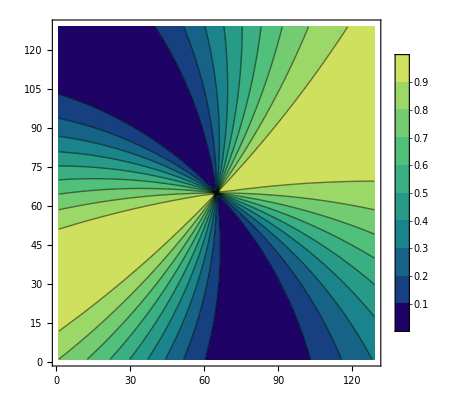

```mathematica
ListContourPlot[intens, ColorFunction->"BlueGreenYellow",PlotLegends->Automatic]
```

```mathematica
Mod[3 Pi, 2 Pi]
```

π

```mathematica
rlv = Table[If[i ==0,{0,0},{i,(Mod[i, Sign[i] * 2 Pi] - i)*-1}],{i,Pi, 5Pi, Pi/32}]
bigxlist = Table[i, {i,Pi,3Pi,Pi/32}];
bigylist = Table[i, {i,3 Pi,5 Pi, Pi/32}];
bigintens=Table[
sperp[bigxlist[[i]],bigylist[[j]],rlv[[i]], rlv[[j]]],
{i,Length[bigxlist]},{j,Length[bigylist]}
];
```

{{π,0},{(33 π)/32,0},{(17 π)/16,0},{(35 π)/32,0},{(9 π)/8,0},{(37 π)/32,0},{(19 π)/16,0},{(39 π)/32,0},{(5 π)/4,0},{(41 π)/32,0},{(21 π)/16,0},{(43 π)/32,0},{(11 π)/8,0},{(45 π)/32,0},{(23 π)/16,0},{(47 π)/32,0},{(3 π)/2,0},{(49 π)/32,0},{(25 π)/16,0},{(51 π)/32,0},{(13 π)/8,0},{(53 π)/32,0},{(27 π)/16,0},{(55 π)/32,0},{(7 π)/4,0},{(57 π)/32,0},{(29 π)/16,0},{(59 π)/32,0},{(15 π)/8,0},{(61 π)/32,0},{(31 π)/16,0},{(63 π)/32,0},{2 π,2 π},{(65 π)/32,2 π},{(33 π)/16,2 π},{(67 π)/32,2 π},{(17 π)/8,2 π},{(69 π)/32,2 π},{(35 π)/16,2 π},{(71 π)/32,2 π},{(9 π)/4,2 π},{(73 π)/32,2 π},{(37 π)/16,2 π},{(75 π)/32,2 π},{(19 π)/8,2 π},{(77 π)/32,2 π},{(39 π)/16,2 π},{(79 π)/32,2 π},{(5 π)/2,2 π},{(81 π)/32,2 π},{(41 π)/16,2 π},{(83 π)/32,2 π},{(21 π)/8,2 π},{(85 π)/32,2 π},{(43 π)/16,2 π},{(87 π)/32,2 π},{(11 π)/4,2 π},{(89 π)/32,2 π},{(45 π)/16,2 π},{(91 π)/32,2 π},{(23 π)/8,2 π},{(93 π)/32,2 π},{(47 π)/16,2 π},{(95 π)/32,2 π},{3 π,2 π},{(97 π)/32,2 π},{(49 π)/16,2 π},{(99 π)/32,2 π},{(25 π)/8,2 π},{(101 π)/32,2 π},{(51 π)/16,2 π},{(103 π)/32,2 π},{(13 π)/4,2 π},{(105 π)/32,2 π},{(53 π)/16,2 π},{(107 π)/32,2 π},{(27 π)/8,2 π},{(109 π)/32,2 π},{(55 π)/16,2 π},{(111 π)/32,2 π},{(7 π)/2,2 π},{(113 π)/32,2 π},{(57 π)/16,2 π},{(115 π)/32,2 π},{(29 π)/8,2 π},{(117 π)/32,2 π},{(59 π)/16,2 π},{(119 π)/32,2 π},{(15 π)/4,2 π},{(121 π)/32,2 π},{(61 π)/16,2 π},{(123 π)/32,2 π},{(31 π)/8,2 π},{(125 π)/32,2 π},{(63 π)/16,2 π},{(127 π)/32,2 π},{4 π,4 π},{(129 π)/32,4 π},{(65 π)/16,4 π},{(131 π)/32,4 π},{(33 π)/8,4 π},{(133 π)/32,4 π},{(67 π)/16,4 π},{(135 π)/32,4 π},{(17 π)/4,4 π},{(137 π)/32,4 π},{(69 π)/16,4 π},{(139 π)/32,4 π},{(35 π)/8,4 π},{(141 π)/32,4 π},{(71 π)/16,4 π},{(143 π)/32,4 π},{(9 π)/2,4 π},{(145 π)/32,4 π},{(73 π)/16,4 π},{(147 π)/32,4 π},{(37 π)/8,4 π},{(149 π)/32,4 π},{(75 π)/16,4 π},{(151 π)/32,4 π},{(19 π)/4,4 π},{(153 π)/32,4 π},{(77 π)/16,4 π},{(155 π)/32,4 π},{(39 π)/8,4 π},{(157 π)/32,4 π},{(79 π)/16,4 π},{(159 π)/32,4 π},{5 π,4 π}}

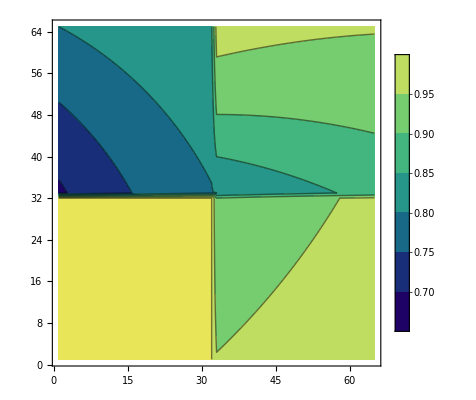

```mathematica
ListContourPlot[bigintens, ColorFunction->"BlueGreenYellow",PlotLegends->Automatic]
```

```mathematica
ArrayPlot[bigintens, ColorFunction->"BlueGreenYellow"]
```

-Graphics-

```mathematica
a = 2; b =1.6; c=1.2;
```

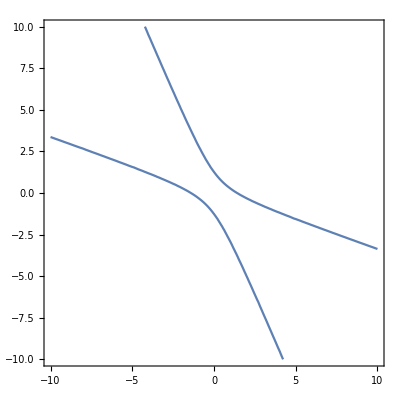

```mathematica
ContourPlot[x^2/a+y^2/b + 2 x y / c==1,{x,-10,10},{y,-10,10}]
```